```mathematica
data=Import["/Users/timur/Documents/5 course/Мат. моделирование/2 семинар/Data.xlsx",{"Data",2}];
Pav=19;
PRR=16.5*10^6;
```

```mathematica
period=(1/PRR)*10^12;(*период сигнала в пс*)
```

```mathematica
data=Delete[data,1];
```

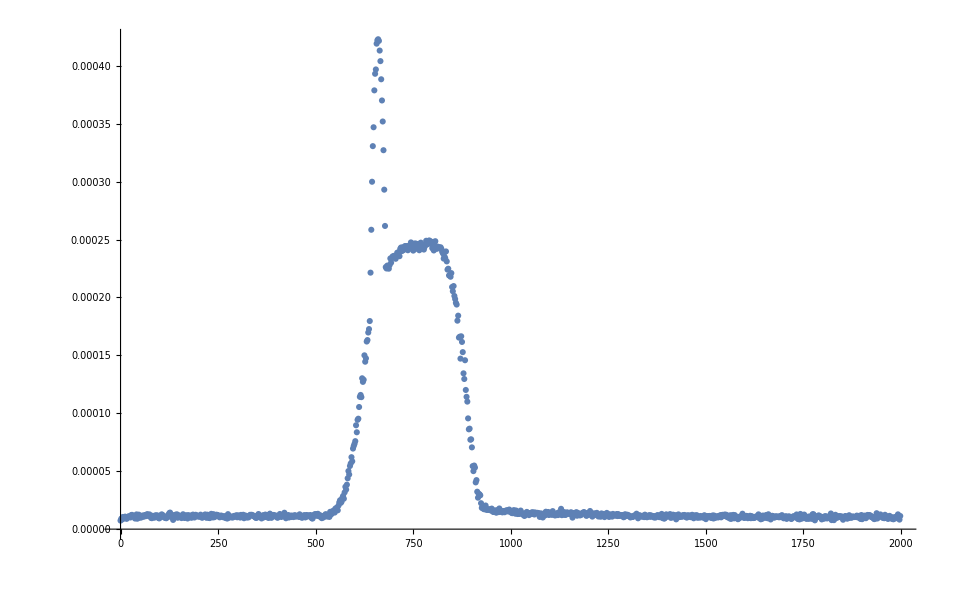

```mathematica
ListPlot[data,PlotRange->All]
```

```mathematica
data[[All,1]];
xs=data[[All,1]];
```

```mathematica
Pick[data[[All,2]],data[[All,1]],1500.];
```

```mathematica
Position[data[[All,1]],1500.][[1,1]]
```

769

```mathematica
(*Среднее значение сигнала от 1500 до 2000 пс*)
```

```mathematica
Pc=Mean[data[[All,2]][[Position[data[[All,1]],1500.][[1,1]];;]]]
```

0.0000105253

```mathematica
xmin=Min[data[[All,1]]];
xmax=Max[data[[All,1]]];
```

```mathematica
(*Полную энергию делим на время, получаем среднюю мощность (все считаем в пс)*)
```

```mathematica
Pavotn=(Integrate[Interpolation[data,InterpolationOrder->3][x],{x,xmin,xmax}]+(period-xmax+xmin)*Pc)/period;
```

```mathematica
Pmax=(Pav/Pavotn)*Max[data[[All,2]]]
```

689.863

```mathematica
(Pav/Pavotn)*Pc
```

17.1705

```mathematica
(*Постоянная сост по-другому*)
```

```mathematica
xleft=1466.796875;
xright=1820.3125;
```

```mathematica
Pcotn=Integrate[Interpolation[data,InterpolationOrder->3][x],{x,xleft,xright}]/(xright-xleft);
```

0.0000105788